```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

ClearAll::wrsym: Symbol Xt is Protected.

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

Remove::rmptc: Symbol Xt is Protected and cannot be removed.

# Male Strategy and Rock-Paper-Scissors

## Game 1

### Payoff Matrix

Three types of males: Orange (aggressive polygamous), Yellow (“sneaky copulator”), and Blue (aggressive mate guarding monogamous).

```mathematica
table = {{"", "O", "Y", "B"}, {"O", "(0,0)", "(-1,1)","(1,-1)"}, {"Y", "(1,-1)", "(0,0)","(-1,1)"}, {"B", "(-1,1)", "(1,-1)","(0,0)"}}
```

{{,O,Y,B},{O,(0,0),(-1,1),(1,-1)},{Y,(1,-1),(0,0),(-1,1)},{B,(-1,1),(1,-1),(0,0)}}

```mathematica
Grid[table,ItemStyle->{FontFamily->"Latin Modern Roman"},Spacings->{2,.75}, Dividers->{{2->True},{2->True}}]
```

| O | Y | B
O | (0,0) | (-1,1) | (1,-1)
Y | (1,-1) | (0,0) | (-1,1)
B | (-1,1) | (1,-1) | (0,0)

### Replicator Dynamics

```mathematica
Subscript[p', 1] = (1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1]
```

p_1 (1-p_1-2 p_2)

```mathematica
Subscript[p', 2] = (-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]
```

p_2 (-1+2 p_1+p_2)

```mathematica
fig1dp := DensityPlot[(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2], {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12},ColorFunction->(ColorData["ThermometerColors"][1.25*#1+.5]&),ColorFunctionScaling->False]
```

```mathematica
fig1s := StreamPlot[{(1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1],(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black]
```

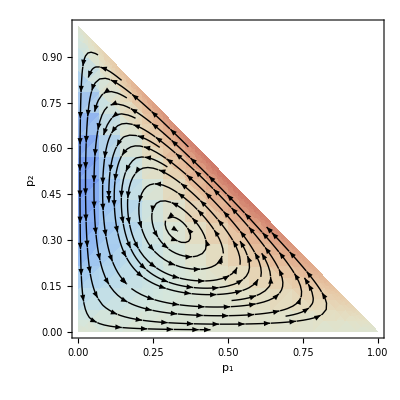

```mathematica
Show[fig1dp, fig1s]
```

### Custom streamDensityPlot Function

```mathematica
streamDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* Created by Jens U.Nöckel for Mathematica 8, updated by @Locus_of_ctrl for StreamPlot 01/2019 *)Module[{img,cont,pL,p,plotRangeRule,densityOptions,streamOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=DensityPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
streamOptions=Join[FilterRules[{opts},FilterRules[Options[StreamPlot],Except[{Prolog,Epilog,FrameTicks,Background,Frame,Axes}]]],{Frame->None,Axes->None}];
(* The density plot img and stream plot cont are created here:*)img=Rasterize[p,"Image"];
cont=If[MemberQ[{0,None},(streams/.FilterRules[{opts},streams])],{},StreamPlot[f,rx,ry,Evaluate@Apply[Sequence,streamOptions]]];
(* Before showing the plots,set the PlotRange for the frame which will be drawn separately: *)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* To align the image img with the stream plot,enclose img in a bounding box rectangle of the same dimensions as cont,
and then combine with cont using Show: *)If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

### Custom streamDensityPlot

```mathematica
streamDensityPlot[{(1-Subscript[p, 1]-2 Subscript[p, 2])Subscript[p, 1],(-1+2 Subscript[p, 1]+Subscript[p, 2])Subscript[p, 2]}, {Subscript[p, 1],0, 1}, {Subscript[p, 2],0, 1},RegionFunction->Function[{x,y},x + y<1], ColorFunction->(ColorData["ThermometerColors"][#1+.5]&),ColorFunctionScaling->False,FrameLabel->{Defer[Subscript[p, 1]], Defer[Subscript[p, 2]]}, PlotRangePadding->None,LabelStyle->Black,BaseStyle->{FontSize->12}, StreamStyle->Black]
```

-Graphics-